## List of Authors

Define a list of authors that we are interested in

```mathematica
authorsDict=Association@{"I.Tambora.1"->"463919","A.Mirizzi.1"->"417997","Georg.G.Raffelt.1"->"429364","Huaiyu.Duan.1"->"397163","G.M.Fuller.1"->"374677","G.M.Fuller.2"->"10042799","G.M.Fuller.3"->"10099942","J.P.Kneller.1"->"436489"}
```

<|I.Tambora.1→463919,A.Mirizzi.1→417997,Georg.G.Raffelt.1→429364,Huaiyu.Duan.1→397163,G.M.Fuller.1→374677,G.M.Fuller.2→10042799,G.M.Fuller.3→10099942,J.P.Kneller.1→436489|>

```mathematica
authorsID=Values@authors
authorsName=Keys@authors
```

{463919,417997,429364,397163,374677,10042799,10099942,436489}

{I.Tambora.1,A.Mirizzi.1,Georg.G.Raffelt.1,Huaiyu.Duan.1,G.M.Fuller.1,G.M.Fuller.2,G.M.Fuller.3,J.P.Kneller.1}

Extract JSON

Construct a fuction to extract json

```mathematica
colPair[authorName_,coauthorName_]:=Module[{authorIDM,coauthorIDM,jsonurlM,rawM,htmlrawM,htmlrenderedM},

authorIDM=Lookup[authorsDict,authorName];

jsonurlM="http://inspirehep.net/author/profile/co-authors?jsondata=%7B%22personId%22%3A%22"<>authorIDM<>"%22%7D";

rawM=Import[jsonurlM,"JSON",CharacterEncoding->"UTF-8"];

htmlrawM="html"/.rawM;
htmlrenderedM=ToString@ImportString[htmlrawM,"HTML"];

StringCases["Georg.G.Raffelt.1 ( 14 )",coauthorName<>" ( "~~(x:DigitCharacter..)->x]/.{}->{0}//ToExpression//First

]
```

Test this function

```mathematica
colPair["I.Tambora.1","Georg.G.Raffelt.1"]
colPair["I.Tambora.1","G.M.Fuller.1"]
```

14

0

Generate Data Table

```mathematica
matTable=Table[colPair[a,b],{a,authorsName},{b,authorsName}]
```

{{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0},{0,0,14,0,0,0,0,0}}

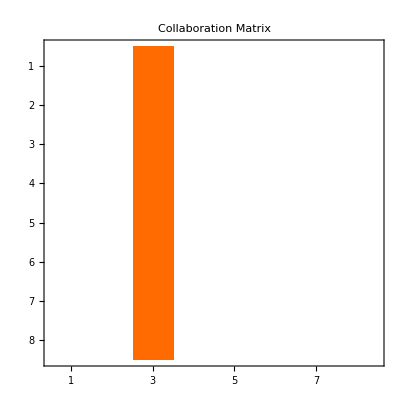

```mathematica
MatrixPlot[matTable,PlotLabel->"Collaboration Matrix"]
```

## Example Program & Test

```mathematica
id="463919";
url="http://inspirehep.net/author/profile/I.Tamborra.1"
jsonurl="http://inspirehep.net/author/profile/co-authors?jsondata=%7B%22personId%22%3A%22"<>id<>"%22%7D"
```

http://inspirehep.net/author/profile/I.Tamborra.1

http://inspirehep.net/author/profile/co-authors?jsondata=%7B%22personId%22%3A%22463919%22%7D

```mathematica
raw=Import[jsonurl,"JSON",CharacterEncoding->"UTF-8"];
```

```mathematica
htmlraw="html"/.raw;
```

```mathematica
htmlrendered=ToString@ImportString[htmlraw,"HTML"];
```

Georg.G.Raffelt.1 ( 14 )

```mathematica
StringCases[htmlrendered,DigitCharacter ..];
StringCases[htmlrendered,WordCharacter ..];
```

```mathematica
StringCases["item13, task15, item11, var4, item2","item"~~(x:DigitCharacter..)->x]
```

{13,11,2}

```mathematica
StringCases["Georg.G.Raffelt.1 ( 14 )","Georg.G.Raffelt.1 ( "~~(x:DigitCharacter..)->x]//ToExpression
```

{14}